# Bridging Elementary Landscapes and a Geometric Theory of Evolutionary Algorithms: First Steps

## Experiments on elementary landscapes for uniform recombination in Boolean spaces with Hamming distance

Marcos Diez García
Department of Computer Science, University of Exeter, Exeter EX4 4QF, UK,
md518@exeter.ac.uk

## Section. Introduction

This Mathematica notebook is the companion of the original paper to be published in the 15th International Conference on Parallel Problem Solving from Nature (PPSN XV) in 2018. Its purpose is to provide the user with implementation details to run simple experiments on two well-known NP combinatorial optimisation problems [1]: Not-All-Equal Satisfiability (NAES) and Weight Partitioning (WP); and two trivial problems: OneMax [2] and LeadingOnes [3-4]. More specifically, to verify:

Whether such problems have elementary landscapes, that is if their fitness functions are eigenfunctions of the uniform recombination Laplacian for some eigenvalue.

What are their discrete nodal domains.

To make the examples simple and intuitive, we will stick to three-dimensional spaces. However, the implementation is ready for the user to experiment with higher dimensions and modify the problem instances to suit their needs.
	This document is organised as follows. Section 2 provides preliminary definitions (e.g. uniform crossover and discrete nodal domain) and auxiliary functions needed in later sections. Sections 3–6 study NAES, WP, one-max and leading-ones, respectively. Section 7 summarises key results.
	DISCLAIMER: The current implementation is not guaranteed to be the ‘fastest’, most ‘correct’ or ‘convenient’. It may contain ‘bugs’ or not work perfectly in all cases. The version of Mathematica used to implement it is 11.2 (Student Edition), there may be certain functionality not available or compatibility issues in earlier or newer versions. Be careful and use it at your own risk. This document is released under the terms of the GNU General Public License version three.

## Section. Preliminary definitions

### Uniform recombination operator for Boolean spaces with Hamming distance

Each binary crossover operator can be defined in terms of a binary ‘mask’, indicating for each bit position of the ‘offspring’ whether the value at that position is taken from the ‘father’ or the ‘mother’. The uniform crossover [5]operator neighbourhood is defined by all possible masks applied to the parents.

```mathematica
masks[dim_]:=Tuples[{0,1},dim];
crossoverMasked[father_,mother_,mask_,dim_]:=
Table[If[mask[[i]]==0,
			father[[i]],
			mother[[i]]],
	 {i,dim}];
unifCrossoverNeigh[father_,mother_,dim_]:= DeleteDuplicates[((crossoverMasked[father,mother,#,dim])&)/@masks[dim]];
```

### Uniform recombination Laplacian

Recombination Laplacians can be seen as a generalisation over the traditional graph Laplacian matrix: -L=D-A defined by the diagonal and adjacency matrices of the underlying graph. Here, we are using Lemma C7 from [5, p. 267] for the uniform recombination Laplacian matrix.

```mathematica
unifCrossoverSmatrix[dim_]:= Table[2*((3/2)^dim)*(3^(-HammingDistance[x,y])),{x,masks[dim]},{y,masks[dim]}];
unifCrossoverLaplacian[dim_]:= ((2*(2^dim))*IdentityMatrix[(2^dim)])-unifCrossoverSmatrix[dim];
```

### Discrete nodal domains

Discrete nodal domains (or sign graphs) [6] allow to algebraically understand how the fitness (eigen-)function is mapped onto the underlying graph of the search space (i.e. the hypercube in our case). That is to understand the connectivity structure amongst fitness values.

```mathematica
(* Positive nodes *)
positiveWeakNodeQ[i_,zeroAvgFitnesses_]:=zeroAvgFitnesses[[i]]≥0;
positiveStrongNodeQ[i_,zeroAvgFitnesses_]:=zeroAvgFitnesses[[i]]>0;

numPositiveWeakNodalDomains[graph_,zeroAvgFitnesses_]:=Length[ConnectedComponents[Subgraph[graph,_?(VertexQ[graph,#]&&positiveWeakNodeQ[#,zeroAvgFitnesses]&)]]];
numPositiveStrongNodalDomains[graph_,zeroAvgFitnesses_]:=Length[ConnectedComponents[Subgraph[graph,_?(VertexQ[graph,#]&&positiveStrongNodeQ[#,zeroAvgFitnesses]&)]]];

(* Negative nodes *)
negativeWeakNodeQ[i_,zeroAvgFitnesses_]:=zeroAvgFitnesses[[i]]≤0;
negativeStrongNodeQ[i_,zeroAvgFitnesses_]:=zeroAvgFitnesses[[i]]<0;

numNegativeWeakNodalDomains[graph_,zeroAvgFitnesses_]:=Length[ConnectedComponents[Subgraph[graph,_?(VertexQ[graph,#]&&negativeWeakNodeQ[#,zeroAvgFitnesses]&)]]];
numNegativeStrongNodalDomains[graph_,zeroAvgFitnesses_]:=Length[ConnectedComponents[Subgraph[graph,_?(VertexQ[graph,#]&&negativeStrongNodeQ[#,zeroAvgFitnesses]&)]]];

(* Visualising nodal domains on the hypercube:
	To easily see the nodal domains each vertex will be labelled with its
  corresponding binary string along with its zero-averaged fitness value.
*)
hypercubeVertexLabel[i_,dim_,zeroAvgFitnesses_]:=ToString[{IntegerString[i-1,2,dim],N[zeroAvgFitnesses[[i]]]}];
nodalDomainsHypercubeLabelled[dim_,zeroAvgFitnesses_]:=Graph[HypercubeGraph[dim],
VertexLabels->Table[i->hypercubeVertexLabel[i,dim,zeroAvgFitnesses],{i,2^dim}],
VertexStyle->Table[i->Which[positiveStrongNodeQ[i,zeroAvgFitnesses],
							Black,
						negativeStrongNodeQ[i,zeroAvgFitnesses],
							White,
						True,
							LightGray],
				{i,2^dim}],
VertexSize->0.2];
(* In higher dimensions the graph can get really cluttered with the labels using the previous
  function ‘nodalDomainsHypercubeLabelled’. The next function displays the graph without the 
  labels.
*)
nodalDomainsHypercubeUnlabelled[dim_,zeroAvgFitnesses_]:=Graph[HypercubeGraph[dim],
VertexStyle->Table[i->Which[positiveStrongNodeQ[i,zeroAvgFitnesses],
							Black,
						negativeStrongNodeQ[i,zeroAvgFitnesses],
							White,
						True,
							LightGray],
				{i,2^dim}],
VertexSize->0.2];
```

### Utility functions for the problems’ implementations

```mathematica
boolify[0]:=False;
boolify[_]:=True;

OtoMinus1[0]:=-1;
OtoMinus1[_]:=1;
```

## Section. Not-all-equal satisfiability (NAES)

### Definition

In the NAES problem we are given a set {x_1,...,x_n} of n binary variables and a set {c_1,...,c_m} of m clauses. Each clause is made of three literals c_i={l_1^i,l_2^i,l_3^i}, where a literal is either a binary variable or its complement l_j^i∈ {x_k,¬x_k}, and it cannot contain both a binary variable and its complement (e.g. {x_1,¬x_1,x_5}). A clause is satisfied if and only if there is at least one true literal and one false literal. The NAES problem is to determine whether there exists an interpretation (i.e. assignment of Boolean values) of the binary variables such that all clauses are satisfied. The fitness of an interpretation is the number of satisfied clauses.

```mathematica
(* satisfiedQ: 
	If {True,False} is a subset of the set 'clause' of Boolean values then we know 
   that there is at least one true literal and one false literal.
*)
satisfiedQ[clause_]:=SubsetQ[clause,{True,False}];
(* interpretations:
	Each clause will be implemented as a n-ary function where the formal parameters represent
  binary variables and the arguments represent their corresponding Boolean value. Thus,
     literals are implicitly encoded as formal parameters. 'interpretations' simply takes one
    assignment 'yesesNoes' and passes it as the argument to each clause function in the set of
    clauses 'clauses', thus returning the list of interpretations for such set of clauses and
    assignment.
*)
interpretations[clauses_,yesesNoes_]:=Table[clauses[[i]]@@yesesNoes,{i,Length[clauses]}];
(* fNAES: the fitness function of not-all-equal satisfiability *)
fNAES[clauses_,onesZeros_]:=
Count[Map[satisfiedQ,
                 interpretations[clauses,boolify/@onesZeros]],
           True];
(* fsNAES: the image of the fitness function, that is all fitness values *)
fsNAES[dim_,clauses_]:=(fNAES[clauses,#]&)/@ Tuples[{0,1},dim];
(* zeroAvgFNAES: The zero-averaged fitness function *)
zeroAvgFNAES[dim_,clauses_,onesZeros_]:=fNAES[clauses,onesZeros]-Mean[fsNAES[dim,clauses]];
```

### Instance example

```mathematica
(* Set of clauses (dimension = 3) *)
dimNAES=3;
clause1[x1_,x2_,x3_]:={x1,!x2,!x3};
clause2[x1_,x2_,x3_]:={!x1,x2,x3};
clause3[x1_,x2_,x3_]:={x1,!x2,x3};
clause4[x1_,x2_,x3_]:={!x1,x2,!x3};
clauses={clause1,clause2,clause4};
(* Instance fitness values *)
fitnessesNAES=fsNAES[dimNAES,clauses];
(* Instance zero-averaged fitness values *)
zeroAvgFitnessesNAES=fitnessesNAES-Mean[fitnessesNAES];
```

### Eigenvalue and discrete nodal domains

First, we want to test whether the zero-averaged fitness function of NAES (f̃)_NAES is an eigenfunction of the uniform recombination Laplacian L_R  for some eigenvalue λ. That is, to test: L_R(f̃)_NAES= λ (f̃)_NAES. We can solve for λ and find its value.

```mathematica
(unifCrossoverLaplacian[dimNAES].zeroAvgFitnessesNAES)/zeroAvgFitnessesNAES
```

{12,12,12,12,12,12,12,12}

This tells us that (f̃)_NAES is elementary with eigenvalue λ=12. In other words:

```mathematica
unifCrossoverLaplacian[dimNAES].zeroAvgFitnessesNAES == 12 * zeroAvgFitnessesNAES
```

True

Secondly, we can also find the order (i.e. spectral position) of λ by just computing the eigenvalues (in non-increasing order) of the Laplacian:

```mathematica
Eigenvalues[unifCrossoverLaplacian[dimNAES]]
```

{14,12,12,12,8,8,8,0}

As expected [7] for the mutation Laplacian, ignoring multiplicities, the NAES landscape for uniform recombination is also elementary for the second smallest non-zero eigenvalue (λ_2); that is, of order p=2.

Finally, we are also interested in finding the discrete nodal domains for (f̃)_NAES. To do it, we only need the fitness function (f̃)_NAES and the graph induced by uniform recombination. Of course, the neighbourhood graph would be a hypergraph [8]. However, uniform recombination spaces have been proved [5] [8] homomorphic to the bit-flip mutation spaces, at least for Boolean sequences. Therefore, all we need is to consider the hypercube and map (f̃)_NAES onto it.

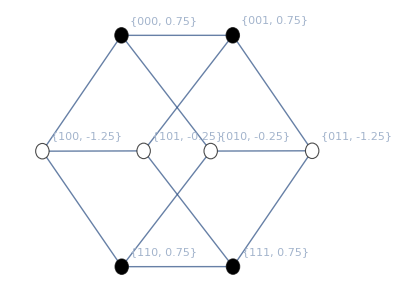

```mathematica
nodalDomainsHypercubeNAES = nodalDomainsHypercubeLabelled[dimNAES,zeroAvgFitnessesNAES]
```

```mathematica
numPositiveWeakNodalDomains[nodalDomainsHypercubeNAES,zeroAvgFitnessesNAES]
```

2

```mathematica
numPositiveStrongNodalDomains[nodalDomainsHypercubeNAES,zeroAvgFitnessesNAES]
```

2

```mathematica
numNegativeWeakNodalDomains[nodalDomainsHypercubeNAES,zeroAvgFitnessesNAES]
```

2

```mathematica
numNegativeStrongNodalDomains[nodalDomainsHypercubeNAES,zeroAvgFitnessesNAES]
```

2

## Section. Weight partition (WP)

### Definition

The WP partition problem is a variant of the classical number partitioning problem. We are given a multiset of n integers {z_1,z_2,…, z_n} and a multiset of ‘weights’ {w_1,w_2,…, w_n} , where each w_i∈{-1,1}  each represents which of the two (mutually exclusive and exhaustive) subsets each integer is assigned to. The problem consists in determining whether there is an assignment of weights to the numbers such that the weighted sum equals zero: ∑_i w_i n_i=0,  and its square attains the minimum precisely at 0.

```mathematica
(* fWP: the fitness function of weight partition *)fWP[dim_,weights_,onesZeros_]:=Sum[weights[[i]]*OtoMinus1[onesZeros[[i]]], {i, 1, dim}]^2;
(* fsWP: the image of the fitness function *)
fsWP[dim_,weights_]:=(fWP[dim,weights,#]&)/@Tuples[{0,1},dim];
(* zeroAvgFWP: the zero-averaged fitness function *)zeroAvgFWP[dim_,weights_,onesZeros_]:=fWP[dim,weights,onesZeros] - Mean[fsWP[dim,weights]];
```

### Instance example

```mathematica
(* Set of weights (dimension = 3) *)
dimWP=3;
weights={1,3,5};
(* Instance fitness values *)
fitnessesWP=fsWP[dimWP,weights];
(* Instance zero-avg fitness values *)
zeroAvgFitnessesWP=fitnessesWP-Mean[fitnessesWP];
```

### Eigenvalue and discrete nodal domains

As for NAES, let us find the eigenvalue for which WP is elementary for the uniform recombination Laplacian:

```mathematica
(unifCrossoverLaplacian[dimWP].zeroAvgFitnessesWP)/zeroAvgFitnessesWP
```

{12,12,12,12,12,12,12,12}

```mathematica
unifCrossoverLaplacian[dimWP].zeroAvgFitnessesWP == 12 * zeroAvgFitnessesWP
```

True

Again, we find that WP is elementary of order p=2 like NAES.

```mathematica
Eigenvalues[unifCrossoverLaplacian[dimWP]]
```

{14,12,12,12,8,8,8,0}

Finally, let us see what are its discrete nodal domains embedded in the hypercube:

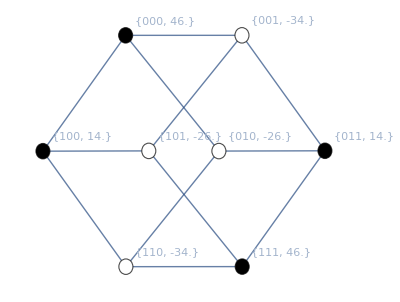

```mathematica
nodalDomainsHypercubeWP=nodalDomainsHypercubeLabelled[dimWP,zeroAvgFitnessesWP]
```

```mathematica
numPositiveWeakNodalDomains[nodalDomainsHypercubeWP,zeroAvgFitnessesWP]
```

2

```mathematica
numPositiveStrongNodalDomains[nodalDomainsHypercubeWP,zeroAvgFitnessesWP]
```

2

```mathematica
numNegativeWeakNodalDomains[nodalDomainsHypercubeWP,zeroAvgFitnessesWP]
```

2

```mathematica
numNegativeStrongNodalDomains[nodalDomainsHypercubeWP,zeroAvgFitnessesWP]
```

2

## Section. One-max

### Definition

The one-max problem simply consists in finding the binary string with maximum number of ones, for a given length (i.e. dimension).

```mathematica
(* fOneMax: the fitness function of one-max *)
fOneMax[dim_,onesZeros_]:=Sum[onesZeros[[i]], {i, 1, dim}];
(* fsOneMax: the image of the fitness function *)
fsOneMax[dim_]:=(fOneMax[dim,#]&)/@Tuples[{0,1},dim];
(* zeroAvgFOneMax: the zero-averaged fitness function *)zeroAvgFOneMax[dim_]:=fsOneMax[dim] - Mean[fsOneMax[dim]];
```

### Instance example

```mathematica
(* Length of the binary string (dimension = 3) *)
dimOneMax=3;
(* Instance fitness values *)
fitnessesOneMax=fsOneMax[dimOneMax];
(* Instance zero-avg fitness values *)
zeroAvgFitnessesOneMax=fitnessesOneMax-Mean[fitnessesOneMax];
```

### Eigenvalue and discrete nodal domains

In this case, we see that one-max is an elementary landscape of order p=1. This means that it is a Fujiyama landscape or single-funnelled (i.e. all local optima are gathered in a single region of the search space).

```mathematica
(unifCrossoverLaplacian[dimOneMax].zeroAvgFitnessesOneMax)/zeroAvgFitnessesOneMax
```

{8,8,8,8,8,8,8,8}

```mathematica
unifCrossoverLaplacian[dimOneMax].zeroAvgFitnessesOneMax == 8 * zeroAvgFitnessesOneMax
```

True

```mathematica
Eigenvalues[unifCrossoverLaplacian[dimOneMax]]
```

{14,12,12,12,8,8,8,0}

The fact that is Fujiyama is reflected in the discrete nodal domains as well. As we can observe, all fitness values above (below) average belong to only one connected subgraph (nodal domain) of the hypercube. Whereas previously, for NAES and WP, we had two separate subgraphs. Moreover, we can appreciate that indeed the nodal domains correspond to Hamming balls of radius 1, centred at 000 and 111.

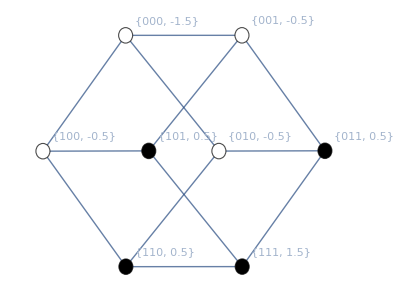

```mathematica
nodalDomainsHypercubeOneMax=nodalDomainsHypercubeLabelled[dimOneMax,zeroAvgFitnessesOneMax]
```

```mathematica
numPositiveWeakNodalDomains[nodalDomainsHypercubeOneMax,zeroAvgFitnessesOneMax]
```

1

```mathematica
numPositiveStrongNodalDomains[nodalDomainsHypercubeOneMax,zeroAvgFitnessesOneMax]
```

1

```mathematica
numNegativeWeakNodalDomains[nodalDomainsHypercubeOneMax,zeroAvgFitnessesOneMax]
```

1

```mathematica
numNegativeStrongNodalDomains[nodalDomainsHypercubeOneMax,zeroAvgFitnessesOneMax]
```

1

## Section. Leading-ones

### Definition

The leading-ones problem consists in maximising the number of contiguous ones appearing at the beginning (left-end) of the binary string.

```mathematica
(* fLO: the fitness function of leading-ones *)
fLO[dim_,onesZeros_]:=Sum[Product[onesZeros[[j]],
                                                                       {j,1,i}], 
                                                       {i, 1, dim}];
(* fsLO: the image of the fitness function *)
fsLO[dim_]:=(fLO[dim,#]&)/@Tuples[{0,1},dim];
(* zeroAvgFLO: the zero-averaged fitness function *)zeroAvgFLO[dim_]:=fsLO[dim] - Mean[fsLO[dim]];
```

### Instance example

```mathematica
(* Length of the binary string (dimension = 3) *)
dimLO=3;
(* Instance fitness values *)
fitnessesLO=fsLO[dimLO];
(* The image of zero-avg fitness function *)
zeroAvgFitnessesLO=fitnessesLO-Mean[fitnessesLO];
```

### Eigenvalue and discrete nodal domains

```mathematica
(unifCrossoverLaplacian[dimLO].zeroAvgFitnessesLO)/zeroAvgFitnessesLO
```

{6,46/7,62/7,74/7,2,-10,70/9,162/17}

For the leading-ones problem we see that the equation L_R(f̃)_LeadingOnes= λ (f̃)_LeadingOnes is not fulfilled. The reason behind is that the leading-ones fitness function is not elementary neither for recombination nor mutation, but a sum of n elementary functions (Walsh functions). However, regardless of whether the landscape is elementary or not, the underlying graph for uniform recombination is still homeomorphic to that of mutation, because being elementary or not only depends on whether the fitness function is an eigenvector of the Laplacian. Therefore, we still can compute the nodal domains on the hypercube. In this case, we observe that it has the same number of discrete nodal domains as one-max, so we know that it is a single-funnelled landscape. However, in this case the discrete nodal domains are arranged in two-dimensional faces corresponding to convex sets {000, 001, 010, 011} and {100, 101, 110, 111} generated by uniform recombination.

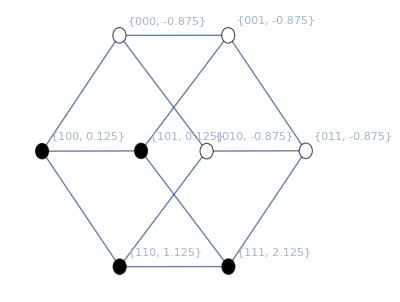

```mathematica
nodalDomainsHypercubeLO=nodalDomainsHypercubeLabelled[dimLO,zeroAvgFitnessesLO]
```

```mathematica
numPositiveWeakNodalDomains[nodalDomainsHypercubeLO,zeroAvgFitnessesLO]
```

1

```mathematica
numPositiveStrongNodalDomains[nodalDomainsHypercubeLO,zeroAvgFitnessesLO]
```

1

```mathematica
numNegativeWeakNodalDomains[nodalDomainsHypercubeLO,zeroAvgFitnessesLO]
```

1

```mathematica
numNegativeStrongNodalDomains[nodalDomainsHypercubeLO,zeroAvgFitnessesLO]
```

1

## Section. Summary of results

```mathematica
(* Figure (a) *)
a1=Legended[nodalDomainsHypercubeUnlabelled[dimNAES,zeroAvgFitnessesNAES],Placed[Style["(a)",FontFamily->"Latin Modern Math",FontSize->16],Below]];
a2=Legended[a1,Placed[Style[Framed["NAES\n(elementary)"],FontFamily->"Latin Modern Math",FontSize->16],Right]];
a3=Legended[a2,Placed[Style["λ_2 = 12\np = 2",FontFamily->"Latin Modern Math",FontSize->16],Right]];
a=Legended[a3,Placed[Style["W_+(f_NAES)\n = W_-(f_NAES)\n = S_+(f_NAES)\n = S_-(f_NAES) = 2",FontFamily->"Latin Modern Math",FontSize->16],Right]];
(* Figure (b) *)
b1=Legended[nodalDomainsHypercubeUnlabelled[dimWP,zeroAvgFitnessesWP],Placed[Style["(b)",FontFamily->"Latin Modern Math",FontSize->16],Below]];
b2=Legended[b1,Placed[Style[Framed["WP\n(elementary)"],FontFamily->"Latin Modern Math",FontSize->16],Right]];
b3=Legended[b2,Placed[Style["λ_2 = 12\np = 2",FontFamily->"Latin Modern Math",FontSize->16],Right]];
b=Legended[b3, Placed[Style["W_+(f_WP)\n = W_-(f_WP)\n = S_+(f_WP)\n = S_-(f_WP) = 2", FontFamily->"Latin Modern Math",FontSize->16], Right]];
(* Figure (c) *)
c1=Legended[nodalDomainsHypercubeUnlabelled[dimOneMax,zeroAvgFitnessesOneMax], Placed[Style["(c)",FontFamily->"Latin Modern Math",FontSize->16],Below]];
c2=Legended[c1,Placed[Style[Framed["One-Max\n(elementary)"],FontFamily->"Latin Modern Math",FontSize->16],Right]];
c3=Legended[c2,Placed[Style["λ_1 = 8\np = 1",FontFamily->"Latin Modern Math",FontSize->16],Right]];
c=Legended[c3,Placed[Style["W_+(f_OneMax)\n = W_-(f_OneMax)\n = S_+(f_OneMax)\n = S_-(f_OneMax) = 1",FontFamily->"Latin Modern Math",FontSize->16],Right]];
(* Figure (d) *)
d1=Legended[nodalDomainsHypercubeUnlabelled[dimLO,zeroAvgFitnessesLO],Placed[Style["(d)",FontFamily->"Latin Modern Math",FontSize->16],Below]];
d2=Legended[d1,Placed[Style[Framed["Leading-Ones\n(not elementary)"],FontFamily->"Latin Modern Math",FontSize->16],Right]];
(*d3=Legended[d2,Placed[Style["p = n",FontFamily->"Latin Modern Math"],Right]];*)
d=Legended[d2,Placed[Style["W_+(f_LeadingOnes)\n = W_-(f_LeadingOnes)\n = S_+(f_LeadingOnes)\n = S_-(f_LeadingOnes) = 1",FontFamily->"Latin Modern Math",FontSize->16],Right]];
```

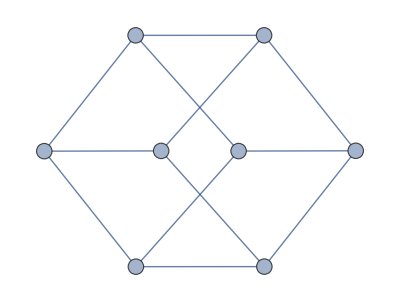
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
g=Grid[{{a,b},{c,d}},Alignment->Left]
```

## References

1.	Grover, L. K.: Local search and the local structure of NP-complete problems. Operations Research Letters 12(4), 235-243 (1992), Elsevier Science Publishers B. V.

2.	Culberson, J. C.: Mutation-Crossover Isomorphisms and the Construction of Discriminating Functions. Evolutionary Computation 2(3), 279-311 (1994), MIT Press.

3.	Rudolph, G.: Convergence properties of evolutionary algorithms. Verlag Dr. Kovac, 1st edn. (1997)

4.	Neumann, F., Sudholt, D., Witt, C.: Analysis of different MMAS ACO algorithms on unimodal functions and plateaus. Swarm Intelligence 3(1), 35-68 (2009), Springer US

5.	Stadler, P. F., Wagner, G. P.: Algebraic Theory of Recombination Spaces. Evolutionary Computation 5(3), 241-275 (1998), MIT Press.

6.	Biyikoglu, T., Leydold, J., Stadler, P. F.: Laplacian Eigenvectors of Graphs: Perron-Frobenius and Faber-Krahn Type Theorems, Lecture Notes in Mathematics, vol. 1915. Springer-Verlag (2007).

7.	Klemm, K., Stadler, P. F.: Rugged and Elementary Landscapes. In: Borenstein, Y., Moraglio, A. (eds.) Theory and Principled Methods for the Design of Metaheuristics, Natural Computing Series, vol. 378, pp. 41-61. Springer Berlin Heidelberg (2014).

8.	Gitchoff, P., Wagner, G. P.: REcombination Induced Hypergraphs: A New Approach to Mutation-Recombination Isomorphism. Complexity 2(1), 37-43 (1996), John Wiley & Sons, Inc.

## Notes

### Elementary Landscapes Testing and Finding Eigen-values (-vectors)

There are other ways to check whether a given fitness function  f is an elementary landscape. Perhaps, the simplest would be to check the if rank of the matrix (Lf
f)is one. If it is true, it means that both vectors are linearly dependent, which happens precisely when Lf is a multiple of f by a factor of λ.

```mathematica
lapOneMax = unifCrossoverLaplacian[dimOneMax];
lapNAES = unifCrossoverLaplacian[dimNAES];
lapWP=unifCrossoverLaplacian[dimWP];
lapLO=unifCrossoverLaplacian[dimLO];
MatrixRank[{lapOneMax.zeroAvgFitnessesOneMax,zeroAvgFitnessesOneMax}]==1
MatrixRank[{lapNAES.zeroAvgFitnessesNAES,zeroAvgFitnessesNAES}]==1
MatrixRank[{lapWP.zeroAvgFitnessesWP,zeroAvgFitnessesWP}]==1
MatrixRank[{lapLO.zeroAvgFitnessesLO,zeroAvgFitnessesLO}]==1
```

True

True

True

False

The disadvantage of this method is that it does not tell us which eigenvalue makes the landscape elementary. Fortunately, there exists an alternative which does, by using the Rayleigh quotient:

R_L_R(f) = ⟨f,L_R f⟩/⟨f,f⟩

Recall that the inner product is zero when the vectors are orthogonal; and, when both vectors form a zero angle, then it equals the product of their norms. Therefore, the Rayleigh quotient can be thought as a measure of how much the transformed fitness function differs from the original, as a measure of distortion caused by the transformation. Of course, for eigenvectors of the transform, this distortion is exactly the eigenvalue. In other words, if the function we input is an eigenfunction, then the Rayleigh quotient is exactly the eigenvalue of that eigenfunction.

```mathematica
(* Input functions *)
y1= zeroAvgFitnessesOneMax;
y2=zeroAvgFitnessesNAES;
y3=zeroAvgFitnessesWP;
y4=zeroAvgFitnessesLO;
(* Rayleigh quotients *)
r1= First[y1.lapOneMax.Transpose[{y1}]/(y1.y1)]
r2= First[y2.lapOneMax.Transpose[{y2}]/(y2.y2)]
r3= First[y3.lapOneMax.Transpose[{y3}]/(y3.y3)]
r4= First[y4.lapOneMax.Transpose[{y4}]/(y4.y4)]
```

8

12

12

618/71

```mathematica
(* Test:
    To test if the Rayleigh quotient is indeed an eigenvalue, we can check if the determinant of the 
    characteristic polynomial (using the Rayleigh quotient as a 'probing eigenvalue'), is zero. If it is
    true, then we know that it is actually an eigenvalue and that the input function is the
    eigenfunction (i.e. an elementary landscape).
 *)
Det[lapOneMax-IdentityMatrix[Length[y1]] r1]==0
Det[lapNAES-IdentityMatrix[Length[y2]] r2]==0
Det[lapWP-IdentityMatrix[Length[y3]] r3]==0
Det[lapLO-IdentityMatrix[Length[y4]] r4]==0
```

True

True

True

False

The reason why this method works as a test is due to a key property of the Rayleigh quotient: it is minimised exactly when the input vector is the eigenfunction of the transform. In other words, eigenvectors are minimisers of the Rayleigh quotient. Therefore, if the fitness function is not elementary this quotient will not be minimal, and so it will not be an eigenvalue.